# Limit Cycles

## Constructed Limit Cycle

```mathematica
(* 1. Equations of motion in polar coordinates *)
{r'[t]==γ(R-r[t]),
θ'[t]==ω}
(* 2. Polar to Cartesian replacement rules *)
{r[t]->√(x[t]^2+y[t]^2),
θ[t]->ArcTan[x[t],y[t]]}
(* 3. Derivatives replacement rules *)
Map[Map[D[#,t]&],%]
(* 4. Apply both sets of replacement rules to EoMs and solve for x'[t], y'[t] *)
Solve[%%%/. %% /. %,{x'[t],y'[t]}][[1]]//FullSimplify
(* 5. In the γ->0 limit this returns linear orbits *)
%/.{γ->0}
```

{r'[t]==γ (R-r[t]),θ'[t]==ω}

{r[t]→√(x[t]^2+y[t]^2),θ[t]→ArcTan[x[t],y[t]]}

{r'[t]→(2 x[t] x'[t]+2 y[t] y'[t])/(2 √(x[t]^2+y[t]^2)),θ'[t]→-(y[t] x'[t])/(x[t]^2+y[t]^2)+(x[t] y'[t])/(x[t]^2+y[t]^2)}

{x'[t]→-ω y[t]+γ x[t] (-1+R/(√(x[t]^2+y[t]^2))),y'[t]→ω x[t]+γ y[t] (-1+R/(√(x[t]^2+y[t]^2)))}

{x'[t]→-ω y[t],y'[t]→ω x[t]}

### Phase diagram

```mathematica
whiteDot=xx↦{Black,PointSize[0.02], Point[xx],White,PointSize[0.015],Point[xx]};
blackDot=xx↦{Black,PointSize[0.02], Point[xx]};
```

```mathematica
Manipulate[
Show[
StreamPlot[{
-ω y+γ x (-1+R/(√(x^2+y^2))),
ω x+γ y (-1+R/(√(x^2+y^2)))
}/.{ω->1},{x,-3,3},{y,-3,3}],
ParametricPlot[If[R>0,1,Null]{R Cos[θ],R Sin[θ]},{θ,0,2π},PlotStyle->Black],
Epilog->If[R>0,whiteDot[{0,0}],blackDot[{0,0}]
]
],
{{γ,0.25},-3,3},{{R,1},-3,3}
]
```

## Predator-Prey Dynamics – Logistic Growth, Saturated Predation

```mathematica
Manipulate[StreamPlot[{
Ar x(1-x/R)-y x/(1+x),
Af y(1-y/x)
},{x,0,15},{y,0,10},AspectRatio->10/15,PlotRangePadding->None,
Epilog->whiteDot[{(Ar (-1+R)-R+√(4 Ar^2 R+(Ar+R-Ar R)^2))/(2 Ar),(Ar (-1+R)-R+√(4 Ar^2 R+(Ar+R-Ar R)^2))/(2 Ar)}/.{Ar->1,R->10}]],
{{Ar,1.},0,3},
{{Af,1./6},0,3},
{{R,10.},0,15}
]
```

### Simulations

#### Load up the RKF45 Sovler

```mathematica
rkf45=Module[{rkf45prime,β,α,c,cHat,cT},
β=N[{{2/9, 0, 0, 0, 0}, {1/12, 1/4, 0, 0, 0}, {69/128, -243/128, 135/64, 0, 0}, {-17/12, 27/4, -27/5, 16/15, 0}, {65/432, -5/16, 13/16, 4/27, 5/144}}];
α=Total/@β;
c={1/9,0,9/20,16/45,1/12,0};
cHat={47/450,0,12/25,32/225,1/30,6/25};
cT=cHat-c;
rkf45prime={f,tol}↦Apply[{t,x,h}↦Module[
{f0,f1,f2,f3,f4,f5,xNext,xHat,hNext,TE},
f0=f[t,x];
f1=f[t+α⟦1⟧h,x+h(β⟦1,1⟧ f0)];
f2=f[t+α⟦2⟧h,x+h(β⟦2,1⟧ f0+β⟦2,2⟧ f1)];
f3=f[t+α⟦3⟧h,x+h(β⟦3,1⟧ f0+β⟦3,2⟧ f1+β⟦3,3⟧ f2)];
f4=f[t+α⟦4⟧h,x+h(β⟦4,1⟧ f0+β⟦4,2⟧ f1+β⟦4,3⟧ f2+β⟦4,4⟧ f3)];
f5=f[t+α⟦5⟧h,x+h(β⟦5,1⟧ f0+β⟦5,2⟧ f1+β⟦5,3⟧ f2+β⟦5,4⟧ f3+β⟦5,5⟧ f3)];
xNext=x+h(c⟦1⟧f0+c⟦2⟧f1+c⟦3⟧f2+c⟦4⟧f3+c⟦5⟧f4);
xHat=x+h(cHat⟦1⟧f0+cHat⟦2⟧f1+cHat⟦3⟧f2+cHat⟦4⟧f3+cHat⟦5⟧f4+cHat⟦6⟧f5);
TE=h(cT⟦1⟧f0+cT⟦2⟧f1+cT⟦3⟧f2+cT⟦4⟧f3+cT⟦5⟧f4+cT⟦6⟧f5);
hNext=0.9 h(tol/Max[Abs[TE]])^(1/5);
If[
Max[Abs[TE]]>tol,
{t,x,hNext,True},
{t+h,xHat,hNext,False}
]
]];
{f,tol}↦Module[{
stepPrime=rkf45prime[{t,x}↦f[t,Sequence@@x],tol]
},
Apply[{t,x,h}↦Most@NestWhile[stepPrime,{t,x,h,True},#⟦4⟧&]]
]
];
```

#### Set up update equation

```mathematica
f={Ar,Af,R}↦{t,x,y}↦{
Ar x(1-x/R)-y x/(1+x),
Af y(1-y/x)
};
initial={0,{1,0.1},1};
update=rkf45[f[1.,1/6.,10.],10^-6];
update[initial]
```

{0.0945975,{1.08337,0.101434},0.0866423}

#### Iterate through a set of initial conditions

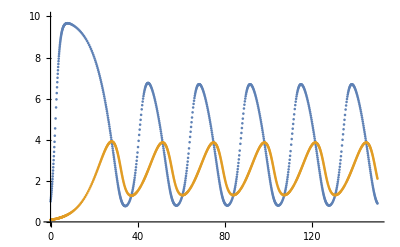

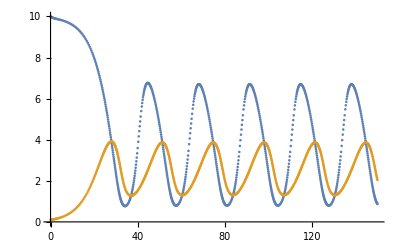

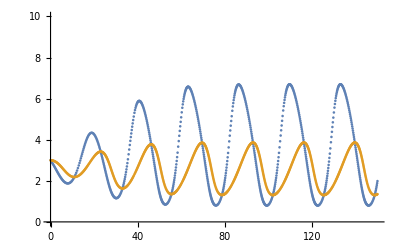

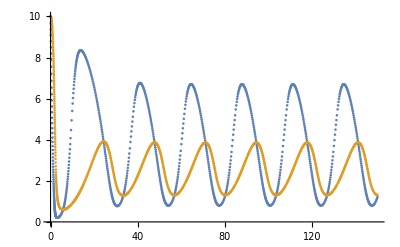

```mathematica
NestWhileList[update,{0,{1,0.1},1},#[[1]]<150&];
Transpose[(s↦{{s[[1]],s[[2,1]]},{s[[1]],s[[2,2]]}})/@%];
ListPlot[%,PlotRange->{0,10}]
NestWhileList[update,{0,{10,0.1},1},#[[1]]<150&];
Transpose[(s↦{{s[[1]],s[[2,1]]},{s[[1]],s[[2,2]]}})/@%];
ListPlot[%,PlotRange->{0,10}]
NestWhileList[update,{0,{3,3},1},#[[1]]<150&];
Transpose[(s↦{{s[[1]],s[[2,1]]},{s[[1]],s[[2,2]]}})/@%];
ListPlot[%,PlotRange->{0,10}]
NestWhileList[update,{0,{10,10},1},#[[1]]<150&];
Transpose[(s↦{{s[[1]],s[[2,1]]},{s[[1]],s[[2,2]]}})/@%];
ListPlot[%,PlotRange->{0,10}]
```

#### Draw stream plot with a trajectory starting arbitrarily close to an outer fixed point

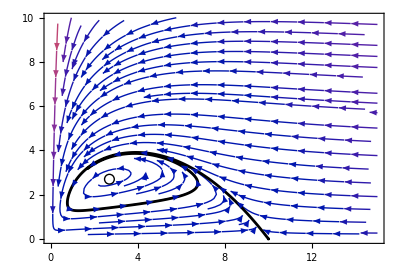

```mathematica
update=rkf45[f[1.,1/6.,10.],10^-6];
NestWhileList[update,{0,{10,10 √($MachineEpsilon)},1},#[[1]]<135&];
(s↦{s[[2,1]],s[[2,2]]})/@%;
Show[
StreamPlot[{
Ar x(1-x/R)-y x/(1+x),
Af y(1-y/x)
}/.{Ar->1,Af->1/6,R->10},{x,0,15},{y,0,10},AspectRatio->10/15,PlotRangePadding->None],
ListLinePlot[%,PlotStyle->Black,PlotRange->Full],
Epilog->whiteDot[{(Ar (-1+R)-R+√(4 Ar^2 R+(Ar+R-Ar R)^2))/(2 Ar),(Ar (-1+R)-R+√(4 Ar^2 R+(Ar+R-Ar R)^2))/(2 Ar)}/.{Ar->1,Af->1/6,R->10}]
]
```